Haley Ittner

```mathematica
sine[x_] = Normal[Series[Sin[x], {x,0,12}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

```mathematica
sine2[x_]= Normal[Series[Sin[2x], {x,0,12}]]
```

2 x-(4 x^3)/3+(4 x^5)/15-(8 x^7)/315+(4 x^9)/2835-(8 x^11)/155925

```mathematica
cosine[x_]= Normal[Series[Cos[x], {x,0,12}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600

```mathematica
Simplify[2sine[x]*cosine[x]- sine2[x]]
```

-(x^13 (-12573792000+237790080 x^2-3350160 x^4+34320 x^6-242 x^8+x^10))/9560105533440000

```mathematica
cosine'[x] + sine[x]
```

0

```mathematica
cos4[x_] = Normal[Series[Cos[x], {x,0,4}]]
```

1-x^2/2+x^4/24

```mathematica
cos8[x_] = Normal[Series[Cos[x], {x,0,8}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

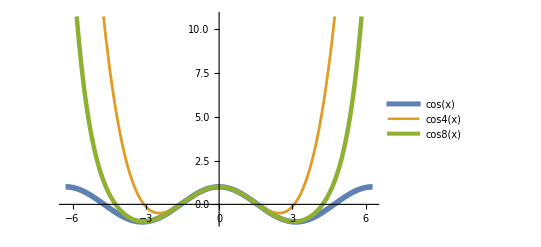

```mathematica
Plot[{Cos[x],cos4[x], cos8[x]},{x,-2Pi,2Pi},PlotStyle -> {{Thickness[.01]}, {Thickness[.005]}, {Thickness[.008]}}, PlotLegends->"Expressions"]
```

```mathematica
cos16[x_] = Normal[Series[Cos[x], {x,0,16}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000

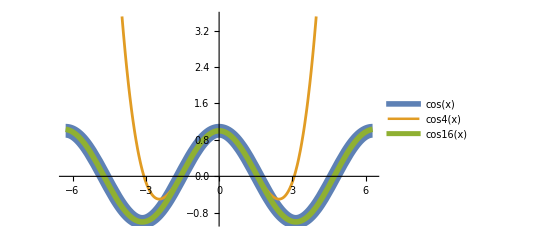

```mathematica
Plot[{Cos[x],cos4[x], cos16[x]},{x,-2Pi,2Pi},PlotStyle -> {{Thickness[.025]}, {Thickness[.005]}, {Thickness[.01]}}, PlotLegends->"Expressions"]
```

```mathematica
cospi[x_] = Normal[Series[Cos[x], {x,Pi,8}]]
```

-1+1/2 (-π+x)^2-1/24 (-π+x)^4+1/720 (-π+x)^6-(-π+x)^8/40320

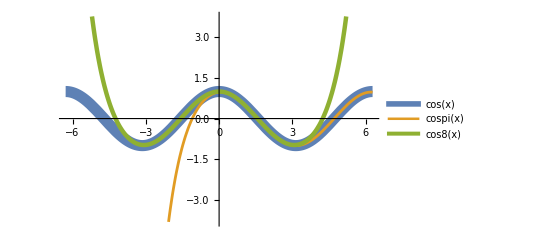

```mathematica
Plot[{Cos[x],cospi[x], cos8[x]},{x,-2Pi,2Pi},PlotStyle -> {{Thickness[.02]}, {Thickness[.005]}, {Thickness[.008]}}, PlotLegends->"Expressions"]
```

```mathematica
y[x_]= Cos[x]-cos8[x]
```

-1+x^2/2-x^4/24+x^6/720-x^8/40320+Cos[x]

```mathematica
q[x_]= Cos[x]-cospi[x]
```

1-1/2 (-π+x)^2+1/24 (-π+x)^4-1/720 (-π+x)^6+(-π+x)^8/40320+Cos[x]

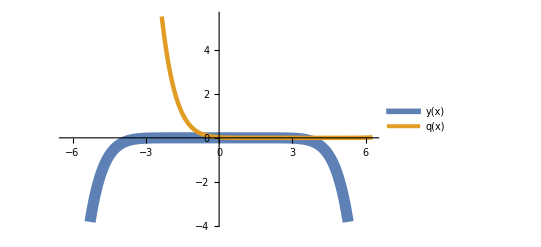

```mathematica
Plot[{y[x],q[x]},{x,-2Pi, 2Pi}, PlotStyle -> {{Thickness[.02]},{Thickness[.008]}}, PlotLegends -> "Expressions"]
```